```mathematica
PrependTo[$Path,"/Users/annils14/Documents/KerrModes"];PrependTo[$Path,"~/Research/KerrQNM/KerrModes"];
Needs["KerrTTMR`"]
SetSpinWeight[2]
SelectMode[PolynomialMode]
```

All KerrMode routines (TTMR) set for Spin-Weight s = 2

Mode set to find Polynomial solutions

```mathematica
<<"Asymptotic00.dat";
```

```mathematica
<<"KerrTTMRTable_00.dat";
```

```mathematica
<<"KerrTTMRTable_01.dat";
```

```mathematica
<<"KerrTTMRTable_02.dat";
```

```mathematica
<<"KerrTTMRTable_03.dat";
```

```mathematica
<<"KerrTTMRTable_04.dat";
```

```mathematica
<<"KerrTTMRTable_05.dat";
```

```mathematica
Save["~/Research/KerrQNM/KerrModes/Asymptotic00.dat",KerrTTMR];
```

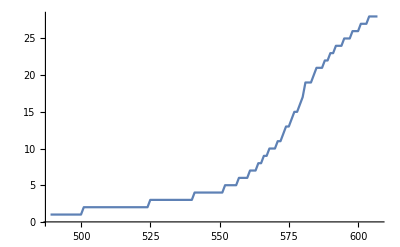

```mathematica
KerrTTMRRefineSequence[2,0,{0,0},-8,PlotRange->All,Index->True,Refinement->{-120,-1}]
```

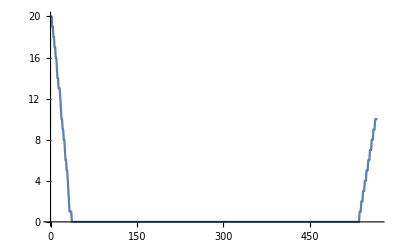

```mathematica
KerrTTMRRefineSequence[2,0,{0,1},-8,PlotRange->All,Index->True,Refinement->{1,-1}]
```

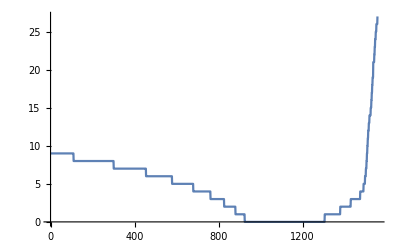

```mathematica
KerrTTMRRefineSequence[2,0,{0,2},-8,PlotRange->All,Index->True,Refinement->{1,-1}]
```

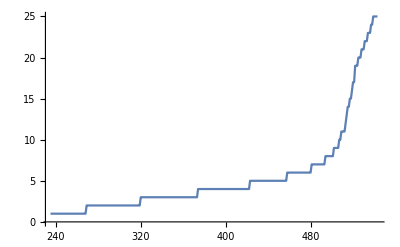

```mathematica
KerrTTMRRefineSequence[3,0,{0,0},-8,PlotRange->All,Index->True,Refinement->{-310,-1}]
```

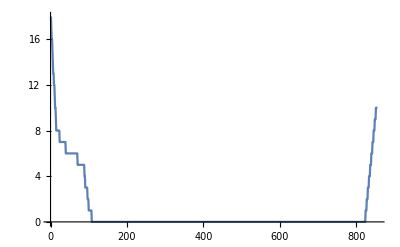

```mathematica
KerrTTMRRefineSequence[3,0,{0,1},-8,PlotRange->All,Index->True,Refinement->{1,-1}]
```

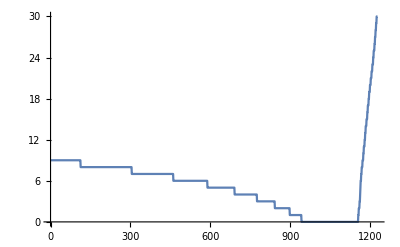

```mathematica
KerrTTMRRefineSequence[3,0,{0,2},-8,PlotRange->All,Index->True,Refinement->{1,-1}]
```

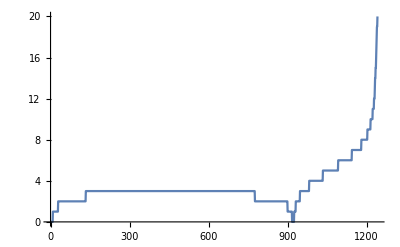

```mathematica
KerrTTMRRefineSequence[4,0,{0,0},-8,PlotRange->All,Index->True,Refinement->{1,-1}]
```

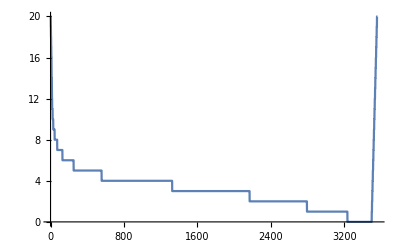

```mathematica
KerrTTMRRefineSequence[4,0,{0,1},-8,PlotRange->All,Index->True,Refinement->{1,-1}]
```

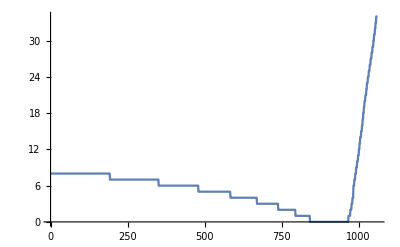

```mathematica
KerrTTMRRefineSequence[4,0,{0,2},-8,PlotRange->All,Index->True,Refinement->{1,-1}]
```

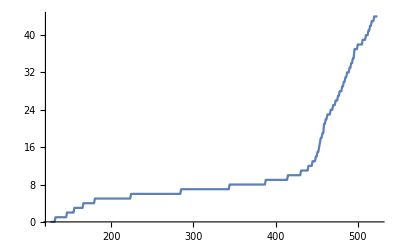

```mathematica
KerrTTMRRefineSequence[5,0,{0,0},-8,PlotRange->All,Index->True,Refinement->{-400,-1}]
```

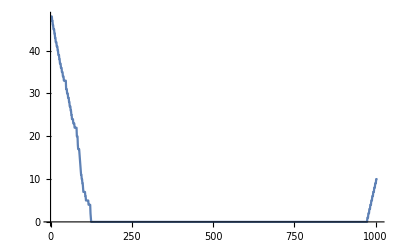

```mathematica
KerrTTMRRefineSequence[5,0,{0,1},-8,PlotRange->All,Index->True,Refinement->{1,-1}]
```

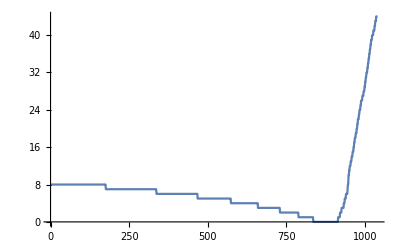

```mathematica
KerrTTMRRefineSequence[5,0,{0,2},-8,PlotRange->All,Index->True,Refinement->{1,-1}]
```

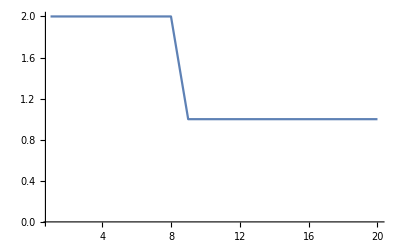

```mathematica
KerrTTMRRefineSequence[5,2,0,-8,PlotRange->All,Index->True,Refinement->{1,20}]
```

```mathematica
ShortenModeSequence[5,2,0,1]
```

Original Length of KerrTTMR[5,2,0] = 1040

Removing first 1 elements

```mathematica
KerrTTMRSequence[5,2,0,-8,SeqDirection->Backward,Minblevel->2,Maxblevel->2]
```

Set $MinPrecision = 24

KerrTTMR[5,2,0] sequence exists with 1039 entries

ModeSol a=0.00075 ω=0.979389-69.9775 ⅈ Alm=24.0006+0.0280218 ⅈ

ModeSol a=0.0005 ω=0.653152-69.99 ⅈ Alm=24.0003+0.0186731 ⅈ

ModeSol a=0.00025 ω=0.326644-69.9975 ⅈ Alm=24.0001+0.00933414 ⅈ

ModeSol a=0. ω=3.27123×10^-47-70. ⅈ Alm=24.

```mathematica
SetOptions[System`ProtoPlotDump`iListPlot,"AllowMicroRanges"->True];
```

```mathematica
Take[KerrOmegaList[5,0,{0,1}],31]
```

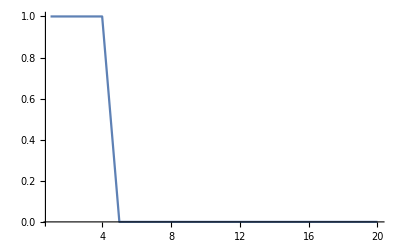

```mathematica
KerrTTMRRefineSequence[4,1,0,-8,PlotRange->All,Maxblevel->0,Minblevel->0,RefinementAction->RemoveLevels,Index->True,Refinement->{1,20}]
```

```mathematica
KerrTTMRSequence[5,2,0,-8,SeqDirection->Backward,Maxblevel->1,Minblevel->1]
```

Set $MinPrecision = 24

KerrTTMR[5,2,0] sequence exists with 1037 entries

ModeSol a=0.0005 ω=0.653152-69.99 ⅈ Alm=24.0003+0.0186731 ⅈ

ModeSol a=0. ω=1.36609×10^-47-70. ⅈ Alm=24.

```mathematica
ShortenModeSequence[5,2,0,1]
```

Original Length of KerrTTMR[5,2,0] = 1038

Removing first 1 elements

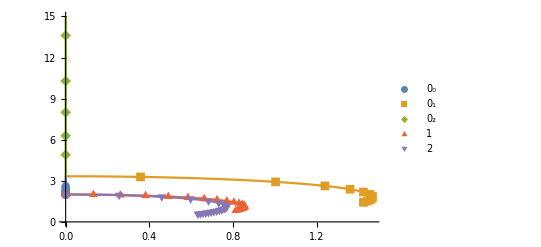

```mathematica
ModePlotOmega[2,0,OTmultiple->{{0,3}},PlotLegends->Automatic,PlotRange->{All,{0,15}}]
```

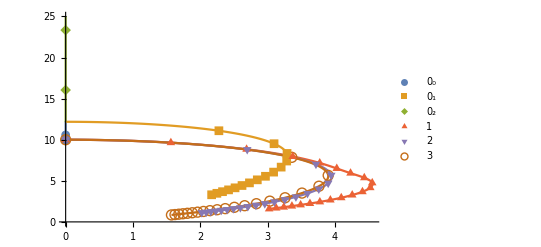

```mathematica
ModePlotOmega[3,0,OTmultiple->{{0,3}},PlotLegends->Automatic,PlotRange->{All,{0,25}}]
```

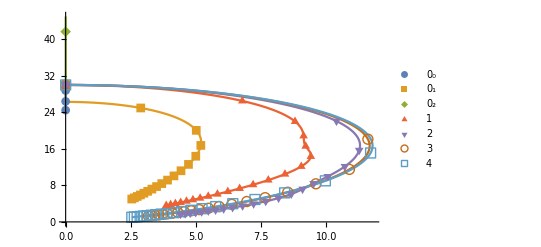

```mathematica
ModePlotOmega[4,0,OTmultiple->{{0,3}},PlotLegends->Automatic,PlotRange->{All,{0,45}}]
```

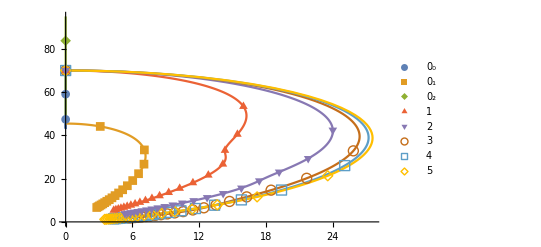

```mathematica
ModePlotOmega[5,0,OTmultiple->{{0,3}},PlotLegends->Automatic,PlotRange->{All,{0,95}}]
```

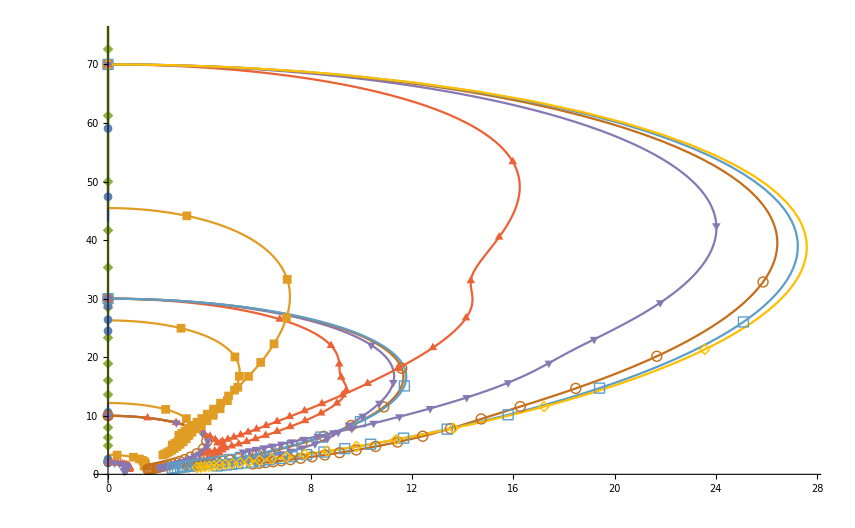

```mathematica
Show[Table[ModePlotOmega[l,0,OTmultiple->{{0,3}},PlotRange->All],{l,2,5}],PlotRange->{All,{0,75}}]
```

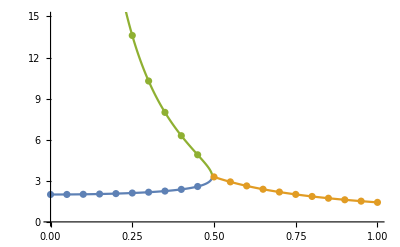

```mathematica
Show[ListLinePlot[Table[KerraOmegaList[2,0,{0,ot},Im],{ot,0,2}]],ListPlot[Table[KerraOmegaListS[2,0,{0,ot},Im],{ot,0,2}]],PlotRange->{0,15}]
```

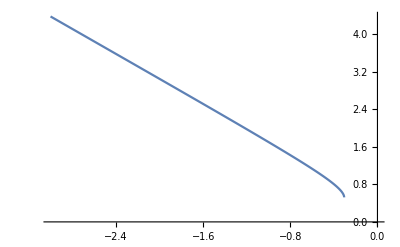

```mathematica
ListLinePlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ KerraOmegaList[2,0,{0,2},Im]]
```

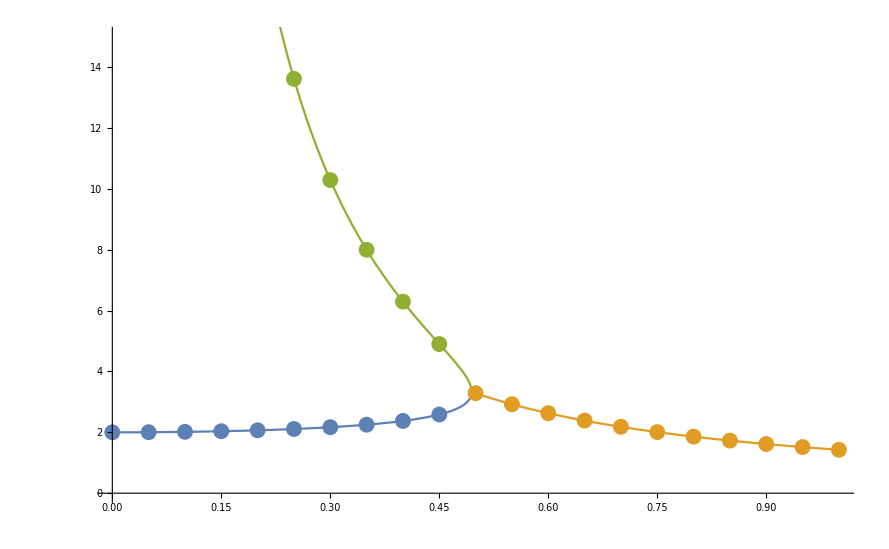

```mathematica
Show[ListLinePlot[Table[KerraOmegaList[2,0,{0,ot},Im],{ot,0,2}]],ListPlot[Table[KerraOmegaListS[2,0,{0,ot},Im],{ot,0,2}]],PlotRange->{0,15}]
```

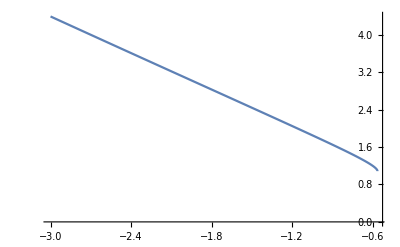

```mathematica
ListLinePlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ KerraOmegaList[3,0,{0,2},Im]]
```

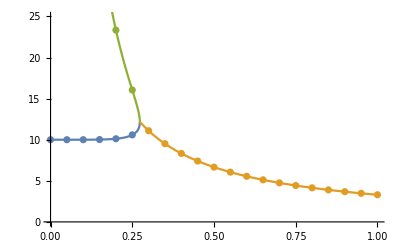

```mathematica
Show[ListLinePlot[Table[KerraOmegaList[3,0,{0,ot},Im],{ot,0,2}]],ListPlot[Table[KerraOmegaListS[3,0,{0,ot},Im],{ot,0,2}]],PlotRange->{0,25}]
```

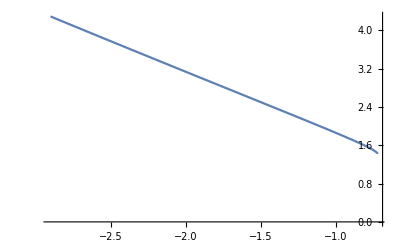

```mathematica
ListLinePlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ KerraOmegaList[4,0,{0,2},Im]]
```

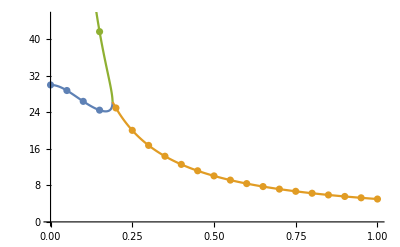

```mathematica
Show[ListLinePlot[Table[KerraOmegaList[4,0,{0,ot},Im],{ot,0,2}]],ListPlot[Table[KerraOmegaListS[4,0,{0,ot},Im],{ot,0,2}]],PlotRange->{0,45}]
```

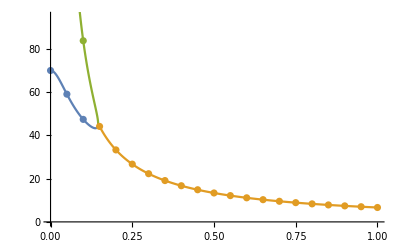

```mathematica
Show[ListLinePlot[Table[KerraOmegaList[5,0,{0,ot},Im],{ot,0,2}]],ListPlot[Table[KerraOmegaListS[5,0,{0,ot},Im],{ot,0,2}]],PlotRange->{0,95}]
```

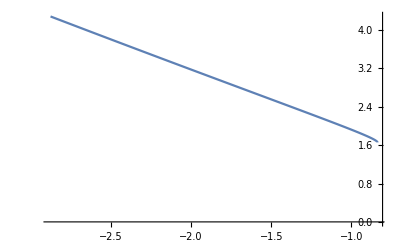

```mathematica
ListLinePlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ KerraOmegaList[5,0,{0,2},Im]]
```

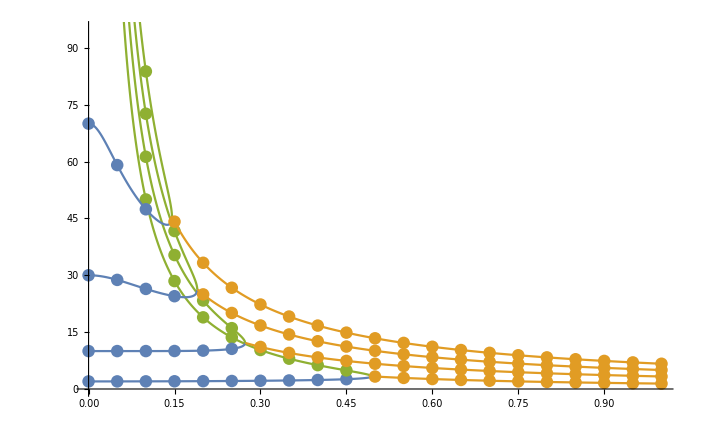

```mathematica
Show[Table[Show[ListLinePlot[Table[KerraOmegaList[l,0,{0,ot},Im],{ot,0,2}],PlotRange->All],ListPlot[Table[KerraOmegaListS[l,0,{0,ot},Im],{ot,0,2}],PlotRange->All],PlotRange->{0,95}],{l,2,5}]]
```

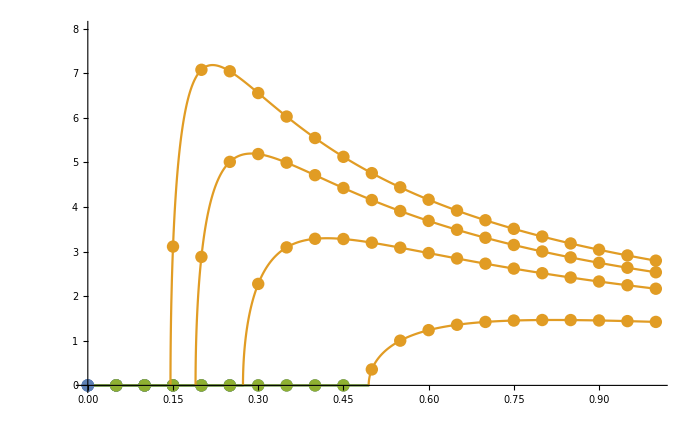

```mathematica
Show[Table[Show[ListLinePlot[Table[KerraOmegaList[l,0,{0,ot},Re],{ot,0,2}]],ListPlot[Table[KerraOmegaListS[l,0,{0,ot},Re],{ot,0,2}]],PlotRange->{0,8}],{l,2,5}]]
```

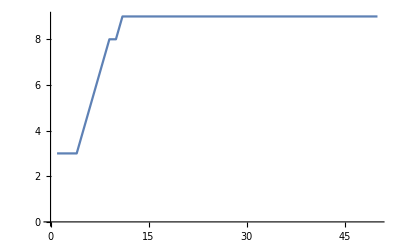

```mathematica
KerrTTMRRefineSequence[3,0,{0,2},-8,Index->True,Refinement->{1,50},PlotRange->All]
```

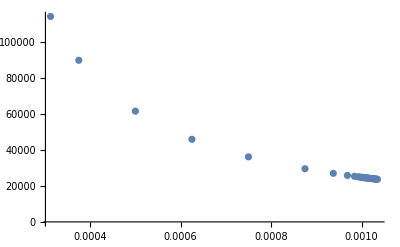

```mathematica
ListPlot[Take[KerraOmegaList[3,0,{0,2},Im],30],PlotRange->All]
```

```mathematica
KerrTTMRSequence[2,0,{0,2},-12,ModePrecision->48,SeqDirection->Backward,MaxΔω->10^99,ExtrapolationOrder->Asymptote,NewtonRadius->10^10,Minblevel->14,SolutionDebug->6,RadialDebug->2]
```

```mathematica
Run["mv ~/Research/KerrQNM/KerrModes/Asymptotic00.dat ~/Research/KerrQNM/KerrModes/Asymptotic00.dat.save"];
Save["~/Research/KerrQNM/KerrModes/Asymptotic00.dat",KerrTTMR];
```

```mathematica
KerrTTMRSequence[3,0,{0,2},-12,ModePrecision->48,SeqDirection->Backward,MaxΔω->10^99,ExtrapolationOrder->Asymptote,NewtonRadius->10^12,Minblevel->14,SolutionDebug->6,RadialDebug->2]
```

```mathematica
Run["mv ~/Research/KerrQNM/KerrModes/Asymptotic00.dat ~/Research/KerrQNM/KerrModes/Asymptotic00.dat.save"];
Save["~/Research/KerrQNM/KerrModes/Asymptotic00.dat",KerrTTMR];
```

```mathematica
KerrTTMRSequence[4,0,{0,2},-12,ModePrecision->48,SeqDirection->Backward,MaxΔω->10^99,ExtrapolationOrder->Asymptote,NewtonRadius->10^12,Minblevel->14,SolutionDebug->6,RadialDebug->2]
```

```mathematica
Run["mv ~/Research/KerrQNM/KerrModes/Asymptotic00.dat ~/Research/KerrQNM/KerrModes/Asymptotic00.dat.save"];
Save["~/Research/KerrQNM/KerrModes/Asymptotic00.dat",KerrTTMR];
```

```mathematica
KerrTTMRSequence[5,0,{0,2},-12,ModePrecision->48,SeqDirection->Backward,MaxΔω->10^99,ExtrapolationOrder->Asymptote,NewtonRadius->10^12,Minblevel->14,SolutionDebug->6,RadialDebug->2]
```

```mathematica
Run["mv ~/Research/KerrQNM/KerrModes/Asymptotic00.dat ~/Research/KerrQNM/KerrModes/Asymptotic00.dat.save"];
Save["~/Research/KerrQNM/KerrModes/Asymptotic00.dat",KerrTTMR];
```

```mathematica
KerrTTMRSequence[2,0,{0,2},-12,ModePrecision->48,SeqDirection->Backward,MaxΔω->10^99,ExtrapolationOrder->Asymptote,NewtonRadius->10^12,Minblevel->15,SolutionDebug->6,RadialDebug->2]
```

```mathematica
Run["mv ~/Research/KerrQNM/KerrModes/Asymptotic00.dat ~/Research/KerrQNM/KerrModes/Asymptotic00.dat.save"];
Save["~/Research/KerrQNM/KerrModes/Asymptotic00.dat",KerrTTMR];
```

```mathematica
KerrTTMRSequence[3,0,{0,2},-12,ModePrecision->48,SeqDirection->Backward,MaxΔω->10^99,ExtrapolationOrder->Asymptote,NewtonRadius->10^12,Minblevel->15,SolutionDebug->6,RadialDebug->2]
```

```mathematica
Run["mv ~/Research/KerrQNM/KerrModes/Asymptotic00.dat ~/Research/KerrQNM/KerrModes/Asymptotic00.dat.save"];
Save["~/Research/KerrQNM/KerrModes/Asymptotic00.dat",KerrTTMR];
```

```mathematica
KerrTTMRSequence[4,0,{0,2},-12,ModePrecision->48,SeqDirection->Backward,MaxΔω->10^99,ExtrapolationOrder->Asymptote,NewtonRadius->10^12,Minblevel->15,SolutionDebug->6,RadialDebug->2]
```

```mathematica
Run["mv ~/Research/KerrQNM/KerrModes/Asymptotic00.dat ~/Research/KerrQNM/KerrModes/Asymptotic00.dat.save"];
Save["~/Research/KerrQNM/KerrModes/Asymptotic00.dat",KerrTTMR];
```

```mathematica
KerrTTMRSequence[5,0,{0,2},-12,ModePrecision->48,SeqDirection->Backward,MaxΔω->10^99,ExtrapolationOrder->Asymptote,NewtonRadius->10^12,Minblevel->15,SolutionDebug->6,RadialDebug->2]
```

```mathematica
Run["mv ~/Research/KerrQNM/KerrModes/Asymptotic00.dat ~/Research/KerrQNM/KerrModes/Asymptotic00.dat.save"];
Save["~/Research/KerrQNM/KerrModes/Asymptotic00.dat",KerrTTMR];
```

```mathematica
KerrTTMRSequence[2,0,{0,2},-12,ModePrecision->48,SeqDirection->Backward,MaxΔω->10^99,ExtrapolationOrder->Asymptote,NewtonRadius->10^12,Minblevel->16,SolutionDebug->6,RadialDebug->2]
```

```mathematica
Run["mv ~/Research/KerrQNM/KerrModes/Asymptotic00.dat ~/Research/KerrQNM/KerrModes/Asymptotic00.dat.save"];
Save["~/Research/KerrQNM/KerrModes/Asymptotic00.dat",KerrTTMR];
```

```mathematica
KerrTTMRSequence[3,0,{0,2},-12,ModePrecision->48,SeqDirection->Backward,MaxΔω->10^99,ExtrapolationOrder->Asymptote,NewtonRadius->10^12,Minblevel->16,SolutionDebug->6,RadialDebug->2]
```

```mathematica
Run["mv ~/Research/KerrQNM/KerrModes/Asymptotic00.dat ~/Research/KerrQNM/KerrModes/Asymptotic00.dat.save"];
Save["~/Research/KerrQNM/KerrModes/Asymptotic00.dat",KerrTTMR];
```

```mathematica
KerrTTMRSequence[4,0,{0,2},-12,ModePrecision->48,SeqDirection->Backward,MaxΔω->10^99,ExtrapolationOrder->Asymptote,NewtonRadius->10^12,Minblevel->16,SolutionDebug->6,RadialDebug->2]
```

```mathematica
Run["mv ~/Research/KerrQNM/KerrModes/Asymptotic00.dat ~/Research/KerrQNM/KerrModes/Asymptotic00.dat.save"];
Save["~/Research/KerrQNM/KerrModes/Asymptotic00.dat",KerrTTMR];
```

```mathematica
KerrTTMRSequence[5,0,{0,2},-12,ModePrecision->48,SeqDirection->Backward,MaxΔω->10^99,ExtrapolationOrder->Asymptote,NewtonRadius->10^12,Minblevel->16,SolutionDebug->6,RadialDebug->2]
```

$Aborted

```mathematica
Run["mv ~/Research/KerrQNM/KerrModes/Asymptotic00.dat ~/Research/KerrQNM/KerrModes/Asymptotic00.dat.save"];
Save["~/Research/KerrQNM/KerrModes/Asymptotic00.dat",KerrTTMR];
```

```mathematica
KerrTTMRRefineSequence[2,0,{0,2},-12,ModePrecision->48,Refinement->{1,4},RefinementAction->RefineAccuracy,SolutionDebug->6,RadialDebug->2]
```

```mathematica
Save["~/Research/KerrQNM/KerrModes/Asymptotic00.dat",KerrTTMR];
```

```mathematica
KerrTTMRRefineSequence[3,0,{0,2},-12,ModePrecision->48,Refinement->{1,4},RefinementAction->RefineAccuracy,SolutionDebug->6,RadialDebug->2]
```

```mathematica
Save["~/Research/KerrQNM/KerrModes/Asymptotic00.dat",KerrTTMR];
```

```mathematica
KerrTTMRRefineSequence[4,0,{0,2},-12,ModePrecision->48,Refinement->{1,4},RefinementAction->RefineAccuracy,SolutionDebug->6,RadialDebug->2]
```

```mathematica
Save["~/Research/KerrQNM/KerrModes/Asymptotic00.dat",KerrTTMR];
```

```mathematica
KerrTTMRRefineSequence[5,0,{0,2},-12,ModePrecision->48,Refinement->{1,4},RefinementAction->RefineAccuracy,SolutionDebug->6,RadialDebug->2]
```

```mathematica
Save["~/Research/KerrQNM/KerrModes/Asymptotic00.dat",KerrTTMR];
```

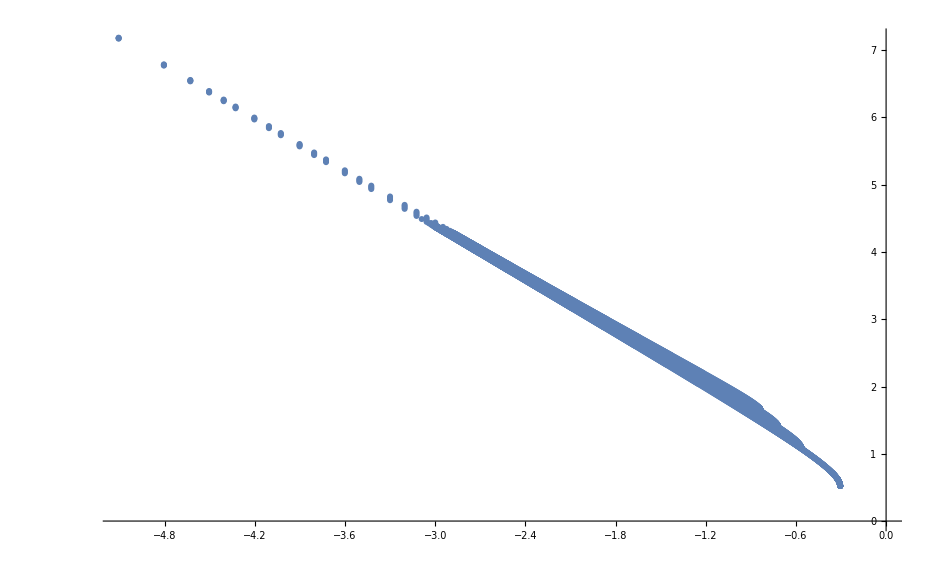

```mathematica
Show[Table[ListPlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ KerraOmegaList[l,0,{0,2},Im]],{l,2,5}]]
```

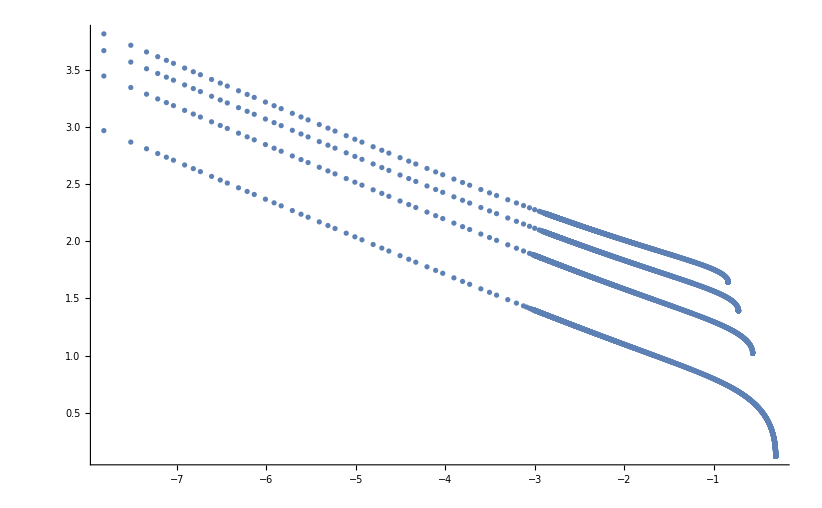

```mathematica
Show[Table[ListPlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ KerraAList[l,0,{0,2},Re]],{l,2,5}],PlotRange->All]
```

```mathematica
tak={0,4,4,4,4};
```

```mathematica
tak={0,8,8,8,8};
```

```mathematica
tak={0,12,12,12,12};
```

```mathematica
tak={0,24,24,24,24};
```

```mathematica
tak={0,30,30,30,30};
```

```mathematica
drp={0,-1100,-770,-720,-720};
```

```mathematica
drp={0,-700,-370,-320,-320};
```

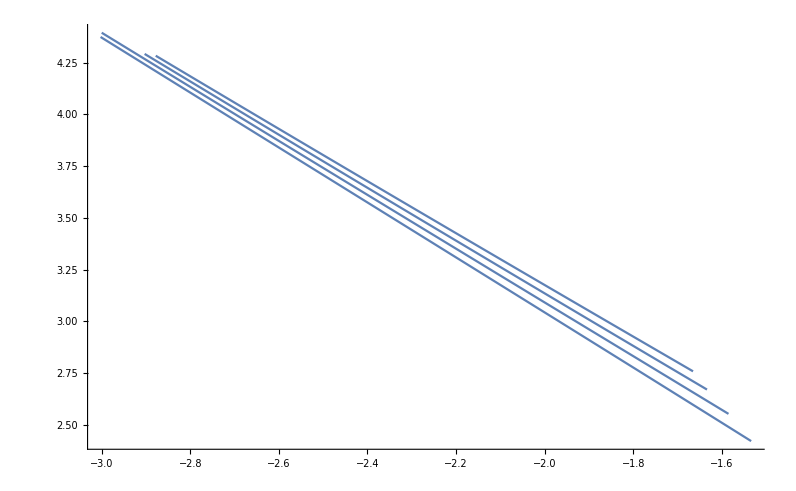

```mathematica
Show[Table[ListLinePlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ Drop[KerraOmegaList[l,0,{0,2},Im],drp[[l]]],PlotRange->All],{l,2,5}],PlotRange->All]
```

```mathematica
ftω=Table[LinearModelFit[{Log10[#[[1]]],Log10[#[[2]]]} & /@ Drop[KerraOmegaList[l,0,{0,2},Im],drp[[l]]],la,la],{l,2,5}]
```

{FittedModel[0.3862346123532501336743702-1.328065540230811335843828 la],FittedModel[0.4748432407086429000036772-1.306334437602855569647236 la],FittedModel[0.5560146798515525847743538-1.28666422739039123371051 la],FittedModel[0.6289127367079171415799919-1.269496469107088711484001 la]}

```mathematica
ftω2=Table[NonlinearModelFit[Drop[KerraOmegaList[l,0,{0,2},Im],drp[[l]]],c1 a^(-4/3),{{c1,2.35}},a],{l,2,5}]
```

{FittedModel[2.34958765116924606596941/a^(4/3)],FittedModel[2.49767667208742393752142/a^(4/3)],FittedModel[2.67717107676240118088775/a^(4/3)],FittedModel[2.84933999175593492540489/a^(4/3)]}

```mathematica
ftω2=Table[NonlinearModelFit[Drop[KerraOmegaList[l,0,{0,2},Im],drp[[l]]],c1 a^(-4/3)+c2 a^(-3/3),{{c1,2.35},c2},a],{l,2,5}]
```

{FittedModel[2.28974614486574482912779/a^(4/3)+0.628504088817443643439193/a],FittedModel[2.28973342894229689293732/a^(4/3)+1.96386680322633094040111/a],FittedModel[2.28968578766734798378432/a^(4/3)+3.30314621069349638678175/a],FittedModel[2.28961880275866503773196/a^(4/3)+4.64517367676861301407823/a]}

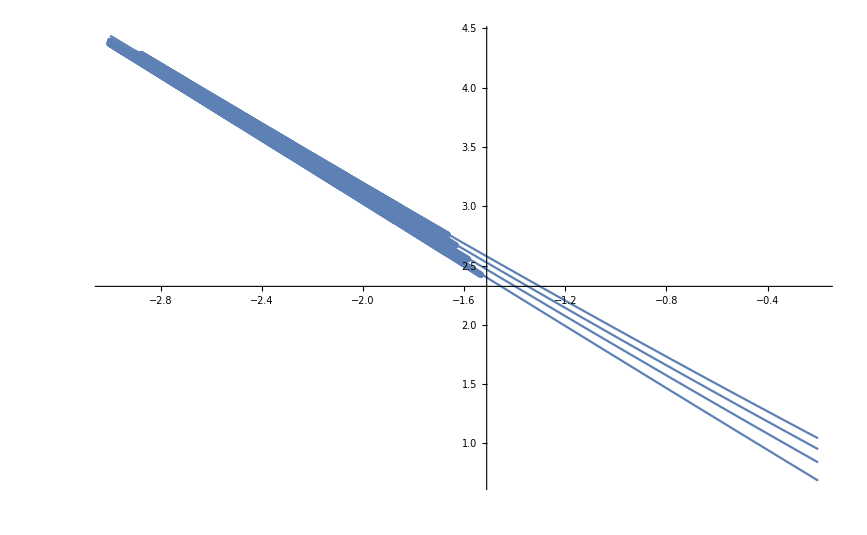

```mathematica
Show[Table[ListPlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ Drop[KerraOmegaList[l,0,{0,2},Im],drp[[l]]]],{l,2,5}],Plot[Table[Log10[ftω2[[t]][10^la]],{t,1,4}],{la,-3,-0.2}],PlotRange->All]
```

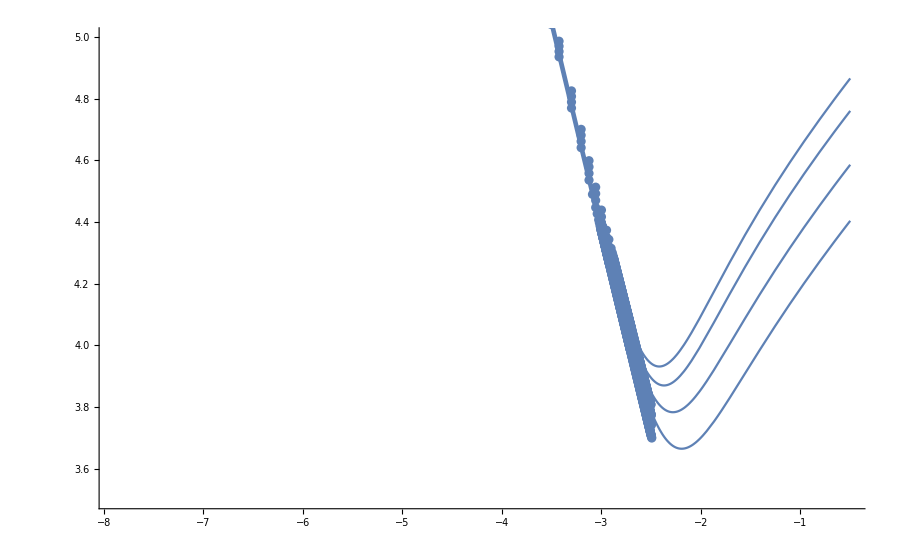

```mathematica
Show[Table[ListPlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ Drop[KerraOmegaList[l,0,{0,2},Im],drp[[l]]],PlotRange->All],{l,2,5}],Plot[Table[Log10[ftω4[[t]][10^la]],{t,1,4}],{la,-7.9,-0.5},PlotRange->All],PlotRange->{3.5,5}]
```

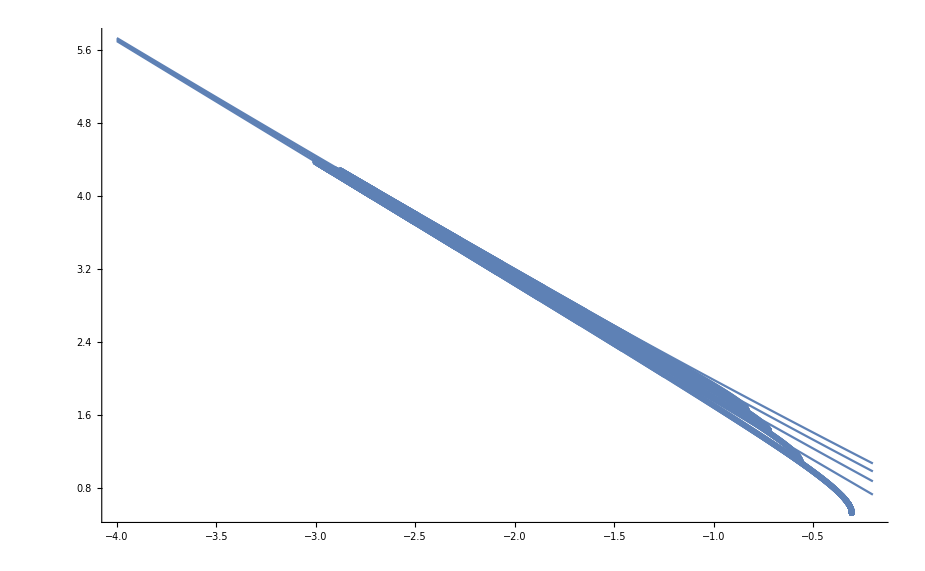

```mathematica
Show[Table[ListPlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ Drop[KerraOmegaList[l,0,{0,2},Im],0drp[[l]]]],{l,2,5}],Plot[Table[Log10[2^(2/3)3^(1/3)(10^la)^(-4/3)+(4/3 l-2)(10^la)^(-1)],{l,2,5}],{la,-4,-0.2}],PlotRange->All]
```

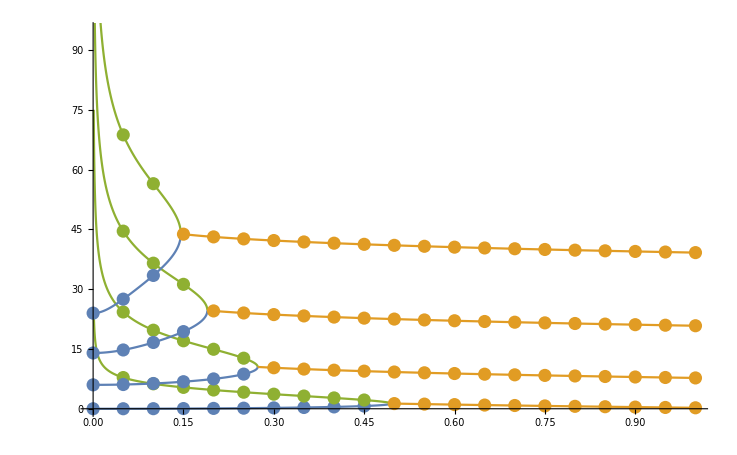

```mathematica
Show[Table[Show[ListLinePlot[Table[KerraAList[l,0,{0,ot},Re],{ot,0,2}],PlotRange->All],ListPlot[Table[KerraAListS[l,0,{0,ot},Re],{ot,0,2}],PlotRange->All],PlotRange->{0,95}],{l,2,5}]]
```

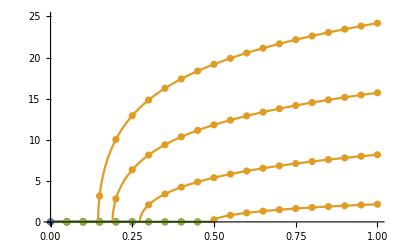

```mathematica
Show[Table[Show[ListLinePlot[Table[KerraAList[l,0,{0,ot},Im],{ot,0,2}],PlotRange->All],ListPlot[Table[KerraAListS[l,0,{0,ot},Im],{ot,0,2}],PlotRange->All],PlotRange->{0,25}],{l,2,5}]]
```

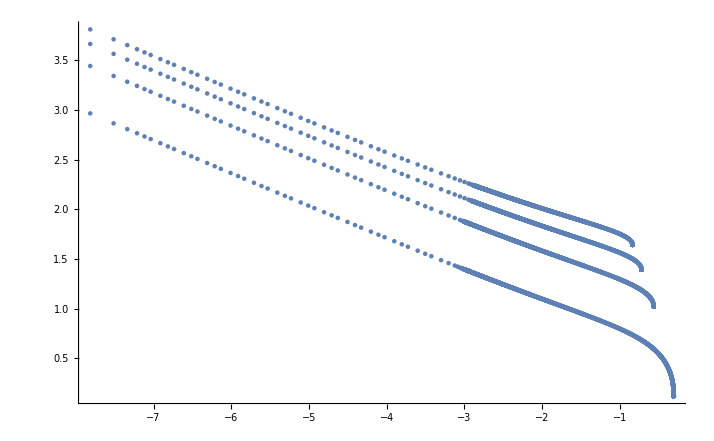

```mathematica
Show[Table[ListPlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ KerraAList[l,0,{0,2},Re],PlotRange->All],{l,2,5}],PlotRange->All]
```

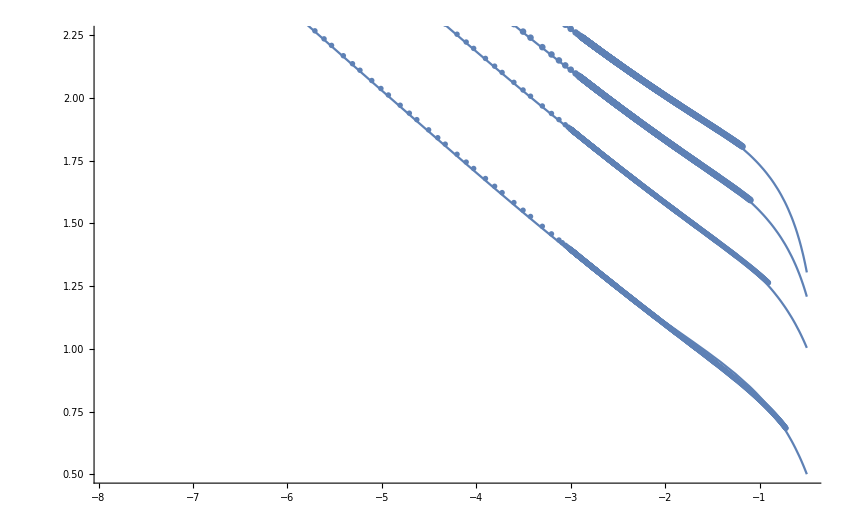

```mathematica
Show[Table[ListPlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ Drop[KerraAList[l,0,{0,2},Re],drp[[l]]],PlotRange->All],{l,2,5}],Plot[Table[Log10[ftA4[[t]][10^la]],{t,1,4}],{la,-7.9,-0.5},PlotRange->All],PlotRange->{0.5,2.25}]
```

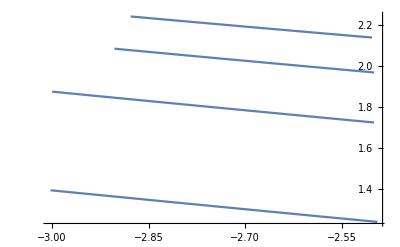

```mathematica
Show[Table[ListLinePlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ Drop[KerraAList[l,0,{0,2},Re],drp[[l]]],PlotRange->All],{l,2,5}],PlotRange->All]
```

```mathematica
ftA=Table[LinearModelFit[{Log10[#[[1]]],Log10[#[[2]]]} & /@ Drop[KerraAList[l,0,{0,2},Re],drp[[l]]],la,la],{l,2,5}]
```

{FittedModel[0.4864497053494418052018781073-0.3027858225302763265779147492 la],FittedModel[0.9753263444477960054182802367-0.2998737111985231045875422944 la],FittedModel[1.252835604908281904834613651-0.2862061814888997455663848889 la],FittedModel[1.454161700965875763006082282-0.2732028694400638699626008458 la]}

```mathematica
10^0.486
```

3.06196

```mathematica
ftA2=Table[NonlinearModelFit[Drop[KerraAList[l,0,{0,2},Re],drp[[l]]],c1 a^(-1/3)+c2 a^(0),{{c1,3.06},c2},a],{l,2,5}]
```

{FittedModel[1.94277423357930068382883+2.28935490665384370549783/a^(1/3)],FittedModel[6.38162458194717448753969479+6.866255830341323611249503885/a^(1/3)],FittedModel[15.1099464742710662985645+11.4449443177817920211836/a^(1/3)],FittedModel[28.1628017753293161545573+16.0246148370319935166975/a^(1/3)]}

```mathematica
ftA3=Table[NonlinearModelFit[Take[KerraAList[l,0,{0,2},Re],tak[[l]]],(2l-3)(2^(2/3)3^(1/3) a^(-1/3)+(4/3 l-2)) +A0+B0 a^(1/3)+C0 a^(2/3),{A0,B0,C0},a],{l,2,5}]
```

{FittedModel[1.91666659216532894683911762423827611954383941358+(2^(2/3) 3^(1/3))/a^(1/3)+0.621891097387154040689767219307375438681468809043 a^(1/3)-3.09277540076073093307418873483684179039576351536 a^(2/3)],FittedModel[0.249999767030516647490034786897526157818162084682+3 (2+(2^(2/3) 3^(1/3))/a^(1/3))+1.99307965691419634962733643170101333205574496811 a^(1/3)-7.72895601251540905567788473620341917230547627776 a^(2/3)],FittedModel[-1.7500004222556743239799270146280839921430296377+5 (10/3+(2^(2/3) 3^(1/3))/a^(1/3))+3.74648942149148478592477187952780156399551459718 a^(1/3)-17.0942405090220577030760306462425659492429325224 a^(2/3)],FittedModel[-4.75000066378335422633882734483592204458545168533+7 (14/3+(2^(2/3) 3^(1/3))/a^(1/3))+6.13693538905146137363723946483209073673638638505 a^(1/3)-31.45841748978545824146369892880956420301636599 a^(2/3)]}

```mathematica
ftA4=Table[NonlinearModelFit[Take[KerraAList[l,0,{0,2},Re],tak[[l]]],(2l-3)(2^(2/3)3^(1/3) a^(-1/3)+(4/3 l-2)+(-39-6 l+2 l^2)/(18 2^(2/3) 3^(1/3))a^(1/3)) +1/4+3/2l-1/2l^2+B0/(2^(2/3) 3^(1/3))a^(1/3)+C0 a^(2/3)+D0 a,{B0,C0,D0},a],{l,2,5}]
```

{FittedModel[23/12+(2^(2/3) 3^(1/3))/a^(1/3)+1.66526269021431117220038641025281816468832492248 a^(1/3)-(43 a^(1/3))/(18 2^(2/3) 3^(1/3))-3.07015331363424436918683122845953937899317729382 a^(2/3)-2.33998919803917205153786038560772956824609595764 a],FittedModel[1/4+3 (2+(2^(2/3) 3^(1/3))/a^(1/3)-(13 a^(1/3))/(6 2^(2/3) 3^(1/3)))+4.83199210094582632424232279451287188035891052368 a^(1/3)-7.65835859935026841498375398770669505221436276077 a^(2/3)-7.29881745218545369553959644732942010526916918945 a],FittedModel[-7/4+5 (10/3+(2^(2/3) 3^(1/3))/a^(1/3)-(31 a^(1/3))/(18 2^(2/3) 3^(1/3)))+7.50733283813181363509745176058035860827381920101 a^(1/3)-16.9664495161289637733242421826850087169573794389 a^(2/3)-13.2075998599017349392464013983860097171031538202 a],FittedModel[-19/4+7 (14/3+(2^(2/3) 3^(1/3))/a^(1/3)-(19 a^(1/3))/(18 2^(2/3) 3^(1/3)))+9.36369250732865704627024904272185219431238678038 a^(1/3)-31.2578232875196529697131327242674094728863087485 a^(2/3)-20.7245363898734250807205699376097811891920323619 a]}

```mathematica
ftA3=Table[NonlinearModelFit[Drop[KerraAList[l,0,{0,2},Re],drp[[l]]],(2l-3)(2^(2/3)3^(1/3) a^(-1/3)+(4/3 l-2)) +A0,{A0},a],{l,2,5}]
```

{FittedModel[1.9165152717337324908333+(2^(2/3) 3^(1/3))/a^(1/3)],FittedModel[0.318022598996985254057679+3 (2+(2^(2/3) 3^(1/3))/a^(1/3))],FittedModel[-1.695648912472081105119104182+5 (10/3+(2^(2/3) 3^(1/3))/a^(1/3))],FittedModel[-4.740552874652499183980994471+7 (14/3+(2^(2/3) 3^(1/3))/a^(1/3))]}

```mathematica
ftA4=Table[NonlinearModelFit[Drop[KerraAList[l,0,{0,2},Re],0drp[[l]]],(2l-3)(2^(2/3)3^(1/3) a^(-1/3)+(4/3 l-2)+(-39-6 l+2 l^2)/(18 2^(2/3) 3^(1/3))a^(1/3)) +1/4+3/2l-1/2l^2+B0/(2^(2/3) 3^(1/3))a^(1/3)+C0 a^(2/3)+D0 a,{B0,C0,D0},a],{l,2,5}]
```

{FittedModel[23/12+(2^(2/3) 3^(1/3))/a^(1/3)+0.680790547708956402781166 a^(1/3)-(43 a^(1/3))/(18 2^(2/3) 3^(1/3))+3.28858266953842591516938 a^(2/3)-10.059788076480460621489 a],FittedModel[1/4+3 (2+(2^(2/3) 3^(1/3))/a^(1/3)-(13 a^(1/3))/(6 2^(2/3) 3^(1/3)))+1.37034758705017881257446 a^(1/3)+18.6737467751624063598279 a^(2/3)-46.0646619956643370357434 a],FittedModel[-7/4+5 (10/3+(2^(2/3) 3^(1/3))/a^(1/3)-(31 a^(1/3))/(18 2^(2/3) 3^(1/3)))-0.242874399647746646293121 a^(1/3)+45.6278277466023462524387 a^(2/3)-116.109942342568586559576 a],FittedModel[-19/4+7 (14/3+(2^(2/3) 3^(1/3))/a^(1/3)-(19 a^(1/3))/(18 2^(2/3) 3^(1/3)))-3.77414753375381886108924 a^(1/3)+81.3377939815208669555725 a^(2/3)-221.967840400081401721946 a]}

```mathematica
ftω3=Table[NonlinearModelFit[Take[KerraOmegaList[l,0,{0,2},Im],tak[[l]]],2^(2/3)3^(1/3) a^(-4/3)+(4/3 l-2)/a+(6A0-21-12 l+4 l^2)/(9 2^(2/3) 3^(1/3))a^(-2/3)+B0 a^(-1/3)+C0,{A0,B0,C0},a],{l,2,5}]
```

{FittedModel[-0.0506227234773074186329453583358158047827723819463+(2^(2/3) 3^(1/3))/a^(4/3)+2/(3 a)-(«98»)/a^(2/3)-0.632772398593938003690775547459681695244030058361/a^(1/3)],FittedModel[-0.0882165988127500425040974635583943358795625529557+(2^(2/3) 3^(1/3))/a^(4/3)+2/a-(«98»)/a^(2/3)-1.93188797570194362481113194297474527994059135884/a^(1/3)],FittedModel[-0.116897636686938704679647642356341674220866110925+(2^(2/3) 3^(1/3))/a^(4/3)+10/(3 a)-(«97»)/a^(2/3)-3.33171933276755173035855239582459935550079959544/a^(1/3)],FittedModel[-0.0114653429192570772087084198953952241156483497144+(2^(2/3) 3^(1/3))/a^(4/3)+14/(3 a)-(«96»)/a^(2/3)-4.89939586932776669607839843463423431176554625807/a^(1/3)]}

```mathematica
ftω4=Table[NonlinearModelFit[Take[KerraOmegaList[l,0,{0,2},Im],tak[[l]]],2^(2/3)3^(1/3) a^(-4/3)+(4/3 l-2)/a+(-39-6 l+2 l^2)/(18 2^(2/3) 3^(1/3))a^(-2/3)+(B0/(3 2^(1/3) 3^(2/3))+(2835-1872l-18l^2+4l^3)/(324 2^(1/3) 3^(2/3))) a^(-1/3)+C0+D0 a^(1/3),{B0,C0,D0},a],{l,2,5}]
```

{FittedModel[-0.0599390617518991732267506953300536114601634768982+(2^(2/3) 3^(1/3))/a^(4/3)+2/(3 a)-43/(18 2^(2/3) 3^(1/3) a^(2/3))-(«97»)/a^(1/3)+0.484439573969578262710827875530664490487248935673 a^(1/3)],FittedModel[-0.117246463940888330773338081668219499902087828745+(2^(2/3) 3^(1/3))/a^(4/3)+2/a-13/(6 2^(2/3) 3^(1/3) a^(2/3))-(«79»)/a^(1/3)+1.51239441969682688722453250566830934756555881769 a^(1/3)],FittedModel[-0.169348820295861380869711503681760655721693992399+(2^(2/3) 3^(1/3))/a^(4/3)+10/(3 a)-31/(18 2^(2/3) 3^(1/3) a^(2/3))-(«78»)/a^(1/3)+2.73368232720258132745757857007376423321213169962 a^(1/3)],FittedModel[-0.0912269576262959239625841990399133233409940568455+(2^(2/3) 3^(1/3))/a^(4/3)+14/(3 a)-19/(18 2^(2/3) 3^(1/3) a^(2/3))-(«78»)/a^(1/3)+4.15848238083334039584206919647741477775127546846 a^(1/3)]}

```mathematica
ftω3=Table[NonlinearModelFit[Drop[KerraOmegaList[l,0,{0,2},Im],drp[[l]]],2^(2/3)3^(1/3) a^(-4/3)+(4/3 l-2)/a+(6A0-21-12 l+4 l^2)/(9 2^(2/3) 3^(1/3))a^(-2/3),{A0},a],{l,2,5}]
```

{FittedModel[(2^(2/3) 3^(1/3))/a^(4/3)+2/(3 a)-1.05062923676862206998989/a^(2/3)],FittedModel[(2^(2/3) 3^(1/3))/a^(4/3)+2/a-0.9682974472044372297174631/a^(2/3)],FittedModel[(2^(2/3) 3^(1/3))/a^(4/3)+10/(3 a)-0.78951389693476428807968/a^(2/3)],FittedModel[(2^(2/3) 3^(1/3))/a^(4/3)+14/(3 a)-0.51573340236180026854511/a^(2/3)]}

```mathematica
ftω4=Table[NonlinearModelFit[Drop[KerraOmegaList[l,0,{0,2},Im],drp[[l]]],2^(2/3)3^(1/3) a^(-4/3)+(4/3 l-2)/a+(-39-6 l+2 l^2)/(18 2^(2/3) 3^(1/3))a^(-2/3)+(B0/(3 2^(1/3) 3^(2/3))+(2835-1872l-18l^2+4l^3)/(324 2^(1/3) 3^(2/3))) a^(-1/3)+C0+D0 a^(1/3),{B0,C0,D0},a],{l,2,5}]
```

{FittedModel[-6860.43147026950890940452+(2^(2/3) 3^(1/3))/a^(4/3)+2/(3 a)-61/(18 2^(2/3) 3^(1/3) a^(2/3))+144.017250765346892003547/a^(1/3)+46951.4573021111724984722 a^(1/3)],FittedModel[-10410.0745424743058034624+(2^(2/3) 3^(1/3))/a^(4/3)+2/a-11/(3 2^(2/3) 3^(1/3) a^(2/3))+215.600306516145491941532/a^(1/3)+71353.7813457930119233987 a^(1/3)],FittedModel[-15811.6581590686954998109+(2^(2/3) 3^(1/3))/a^(4/3)+10/(3 a)-67/(18 2^(2/3) 3^(1/3) a^(2/3))+295.8453128430452043332/a^(1/3)+107100.517393927655240671 a^(1/3)],FittedModel[-20173.3901752771321543519+(2^(2/3) 3^(1/3))/a^(4/3)+14/(3 a)-(16 (2/3)^(1/3))/(9 a^(2/3))+371.007209540342744448971/a^(1/3)+136556.022219502513311327 a^(1/3)]}

```mathematica
Clear[Adiff];Adiff[l_]:=ADiff[l]={#[[1]],#[[2]]-((2l-3)(2^(2/3)3^(1/3) #[[1]]^(-1/3)+(4/3 l-2)+(-39-6 l+2 l^2)/(18 2^(2/3) 3^(1/3))#[[1]]^(1/3))+1/4+3/2l-1/2l^2 +(-207/10+223/15l-l^2)/(8 2^(-1/3) 3^(-2/3))#[[1]]^(1/3)) }& /@KerraAList[l,0,{0,2},Re];
```

```mathematica
Simplify[(-207/10+223/15l-l^2)/(8 2^(-1/3) 3^(-2/3))-A0fit2[l]]
```

7.233339472214393399383447631506594954×10^-8-1.61755614643288257573108752698008054508×10^-7 l+1.43909749429630651689308111821875382634×10^-8 l^2

```mathematica
A0fit[l]
```

-6.85644124576047985296+5.8886491804241404679836 l-1.05520754336182365614735 l^2

```mathematica
N[59/12]
```

4.91667

```mathematica
N[Apart[2^(-1/3) 3^(-2/3)A0fit[l]8]]
```

-20.7+14.8667 l-1. l^2

```mathematica
1/(8 2^(-1/3) 3^(-2/3))
```

1/4 (3/2)^(2/3)

```mathematica
20+7/10
```

207/10

```mathematica
InputForm[Factor[(-207/10+223/15l-l^2)/(8 2^(-1/3) 3^(-2/3))]]
```

-(621 - 446*l + 30*l^2)/(40*2^(2/3)*3^(1/3))

```mathematica
Apart[-(621 - 446*l + 30*l^2)/40]
```

-621/40+(223 l)/20-(3 l^2)/4

```mathematica
dfit=Table[NonlinearModelFit[Take[Adiff[l],8],B0 a^(1/3)+C0 a^(2/3)+D0 a,{B0,C0,D0},a],{l,2,5}]
```

```mathematica
A0fit=NonlinearModelFit[{#+1,dfit[[#]]["BestFitParameters"][[1,2]]} & /@ {1,2,3,4},a0+a1 l+a2 l^2,{a0,a1,a2},l]
```

FittedModel[-6.78116781451174820571816259352836678721397+4.87021055470428807692152858956370867699135 l-0.327592549424061379014067239471243631100723 l^2]

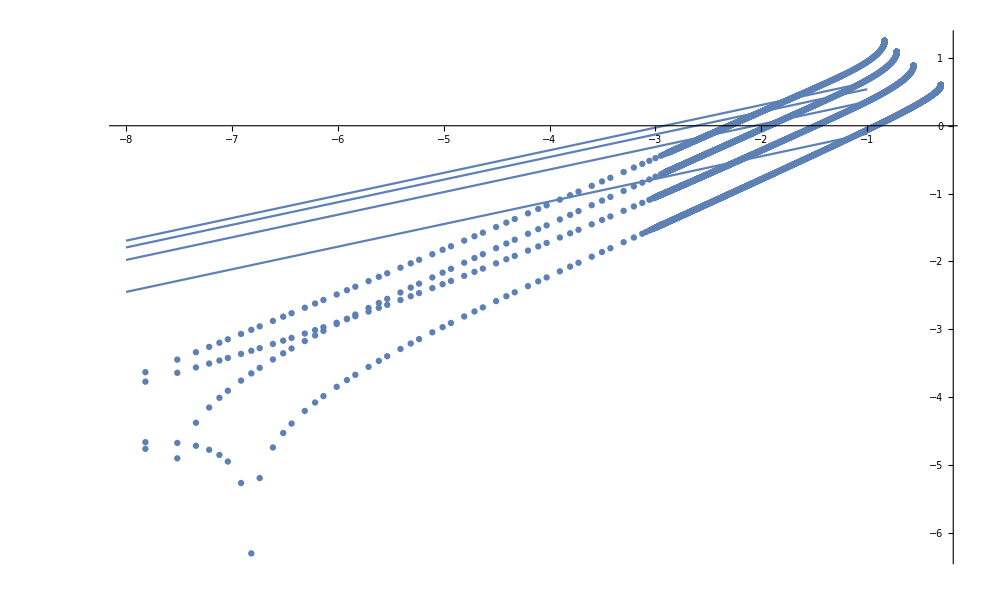

```mathematica
Show[Table[ListPlot[{Log10[#[[1]]],Log10[Abs[#[[2]]]]} & /@ Adiff[l],PlotRange->All],{l,2,5}],Plot[Table[Log10[(-6.7811678+4.870210 l-0.32759254942 l^2)(10^la)^(1/3)],{l,2,5}],{la,-8,-1},PlotRange->All],PlotRange->All]
```

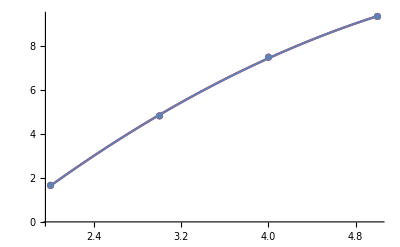

```mathematica
Show[ListPlot[{#+1,ftω4[[#]]["BestFitParameters"][[1,2]]} & /@ {1,2,3,4},PlotStyle->Red],Plot[{A0fit2[l]},{l,2,5},PlotStyle->Red],ListPlot[{#+1,ftA4[[#]]["BestFitParameters"][[1,2]]} & /@ {1,2,3,4}],Plot[{A0fit[l]},{l,2,5}]]
```

```mathematica
Fit[{#+1,ftA3[[#]]["BestFitParameters"][[1,2]]} & /@ {1,2,3,4},{1,l,l^2},l]
```

0.0624192868133589748482731+1.622628971726293085529068 l-0.50772033097097727172868806 l^2

```mathematica
Fit[{#+1,ftA3[[#]]["BestFitParameters"][[1,2]]} & /@ {1,2,3,4},{1,Sqrt[l]},l]
```

11.6647783070201888870552584-6.92322235625211852874517654 √l

```mathematica
{#+1,ftω4[[#]]["BestFitParameters"]} & /@ {1,2,3,4}
```

{{2,{B0→1454.63195738751964126135501684759415094789707287,C0→-134311.660323850576530016100640049266828248595355,D0→1.39864203270736825253410071786113764786135077375×10^7}},{3,{B0→2183.62684852601117733737303699884393615697949616,C0→-201467.517826432463838756920375170301324765435178,D0→2.09796312767470132202255032408967700809946880624×10^7}},{4,{B0→2911.69356042677106190239876836076579375384695732,C0→-268623.370122387715202635687661945936159354624671,D0→2.79728424195257012085406247527543960243180474042×10^7}},{5,{B0→3638.50450038025362735568427155406803839320147011,C0→-335779.092201773305535427907482247034930705135159,D0→3.49660537669183728435995010618521460891513792896×10^7}}}

```mathematica
{#+1,ftA4[[#]]["BestFitParameters"]} & /@ {1,2,3,4}
```

{{2,{B0→1441.59470412589716424717223859382864585710076205,C0→-452473.40346619536035150394044009736030143118684,D0→4.66656167904863411160897797317019823726557291628×10^7}},{3,{B0→2166.03652476524549757741915487705365092616059582,C0→-678713.15822875511905535331909850217149686499773,D0→6.99984213841179846433133667349030436184056099102×10^7}},{4,{B0→2890.86053695538966537080393315065924437539937935,C0→-904957.632748980999558577386836533513612064780523,D0→9.33312250113035095803915847412427732519671304166×10^7}},{5,{B0→3615.73914810346391369889992594582254408762777891,C0→-1.13120709031843734720822662266172246042985673331×10^6,D0→1.16664027000220411373750876711792027408346807245×10^8}}}

```mathematica
A0fit2=NonlinearModelFit[{#+1,ftω3[[#]]["BestFitParameters"][[1,2]]} & /@ {1,2,3,4},a0+a1 l+a2 l^2,{a0,a1,a2},l]
```

FittedModel[0.136083 l (-15.0644 ftω3⟦1⟧[BestFitParameters]⟦1,2⟧+12.125 ftω3⟦2⟧[BestFitParameters]⟦1,2⟧+13.5947 ftω3⟦3⟧[BestFitParameters]⟦1,2⟧-10.6553 ftω3⟦4⟧[BestFitParameters]⟦1,2⟧)+0.5 «1»+0.0319765 l^2 («5»+«1»)]

```mathematica
A0fit=NonlinearModelFit[{#+1,ftA3[[#]]["BestFitParameters"][[1,2]]} & /@ {1,2,3,4},a0+a1 l+a2 l^2,{a0,a1,a2},l]
```

FittedModel[0.250000108205102524576930255595328435509504824019+1.49999994964096092283346760830925036118606342252 l-0.500000020764883567419121039883438689345852846347 l^2]

```mathematica
A0fit=NonlinearModelFit[{#+1,ftA3[[#]]["BestFitParameters"][[1,2]]} & /@ {1,2,3,4},a0/3+a1(3/2 l-1/2 l^2),{a0,a1},l]
```

FittedModel[0.307771700327719768937520719344521906658578213221+0.972891382169256242805106527222321889936830401217 ((3 l)/2-l^2/2)]

```mathematica
A0fit2=NonlinearModelFit[{#+1,ftω4[[#]]["BestFitParameters"][[1,2]]} & /@ {1,2,3,4},a0+a1 l+a2 l^2,{a0,a1,a2},l]
```

FittedModel[-15.5250001656021343013403328463011014727756239158+11.1500003703279117902807090686210813207911045075 l-0.750000032947107962875886847235444119420860541096 l^2]

```mathematica
A0fit=NonlinearModelFit[{#+1,ftA4[[#]]["BestFitParameters"][[1,2]]} & /@ {1,2,3,4},a0+a1 l+a2 l^2,{a0,a1,a2},l]
```

FittedModel[-15.5249976270871251354303761606716890942423585457+11.1499976547866407147085269380824063683771260035 l-0.749999453072833507585179206244984050465716193599 l^2]

```mathematica
Rationalize[0.47]
```

47/100

```mathematica
A0fit2["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
a0 | -15.5250001656021343013403328463011014727756239158 | 0.96266258135035514310334305585430525653795519 | {-27.7567880160941837214351186216756813445209085,-3.2932123151100848812455470709265216010303394}
a1 | 11.1500003703279117902807090686210813207911045075 | 0.59174017713388902917173702193220726913236666 | {3.6312285290444323435373596712345256526986282,18.6687722116113912370240584660076369888835808}
a2 | -0.750000032947107962875886847235444119420860541096 | 0.083852571574924514343329261011071440359685237 | {-1.81544797503284223970260180523437245283747936,0.31544790913862631395082811076348421399575828}

```mathematica
A0fit2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a0 | 0.249995007445366328651926471350328439463926704793 | 2.056968161896764594804386646578565168×10^-8 | 1.215356718087662423317690306820687021×10^7 | 5.238131018597464818964908547790363433×10^-8
a1 | 1.50000277420181407281220086223751862446260684141 | 1.264400141919064074049088097066200315×10^-8 | 1.18633549971384868364715747422729229×10^8 | 5.366270945454619519455648205097726721×10^-9
a2 | -0.499999499297014473873429049280075616527013777713 | 1.79171885730557525107630430280465999×10^-9 | -2.790613590175214799483216172945725036×10^8 | 2.281289586666170326367159501189120718×10^-9

```mathematica
A0fit["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
a0 | -6.85644124576047985296 | 0.49381737832093582218 | {-13.130985956987330515,-0.5818965345336291909}
a1 | 5.8886491804241404679836 | 0.30354517624392283503 | {2.0317420243906226977,9.74555633645765823823}
a2 | -1.05520754336182365614735 | 0.043013884472910360865 | {-1.60175076597278887253,-0.50866432075085843976}

```mathematica
A0fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a0 | 0.250006280372801284576662928427938967977226394717 | 1.33011175011501178073087604416869923948×10^-6 | 187958.854097171761743186079962902838426 | 3.3870166713851761552555247167845652784×10^-6
a1 | 1.49999684302099582022925385379907238326004408362 | 8.17607932279722699934570440564806011168×10^-7 | 1.83461630422124132996853676334747448467×10^6 | 3.47004314146085665407010646177317340435×10^-7
a2 | -0.500001016430337135948467506993066898251944515682 | 1.15859173182690974737849906281354801611×10^-7 | -4.31559282441898041412476878290558457251×10^6 | 1.47516181036675937898754848038386498291×10^-7

```mathematica
N[(2^(2/3) 3^(1/3))]
```

2.28943

```mathematica
ω[a_,l_]:=-(2^(2/3)3^(1/3) a^(-4/3)+(4/3 l-2)/a+(6(0.3015+1.5 l-0.6 l^2)-21-12 l+4 l^2)/(9 2^(2/3) 3^(1/3))a^(-2/3))ⅈ
```

```mathematica
ω[a_,l_]:=-(2^(2/3)3^(1/3) a^(-4/3)+(4/3 l-2)/a+(6(1/4+3/2 l-1/2 l^2)-21-12 l+4 l^2)/(9 2^(2/3) 3^(1/3))a^(-2/3))ⅈ
```

```mathematica
Alm[a_,l_]:=(2l-3)(2^(2/3)3^(1/3) a^(-1/3)+(4/3 l-2)) +1/4+3/2 l-1/2 l^2
```

```mathematica
Fit[{Log10[#[[1]]],Log10[Abs[ⅈ ω[#[[1]],2]-#[[2]]]]} & /@ Take[KerraOmegaList[2,0,{0,2},Im],tak[[2]]] ,{1,la},la]
```

-0.196118139279219559723728374516577950679-0.3329477285788464834692911895274064858295 la

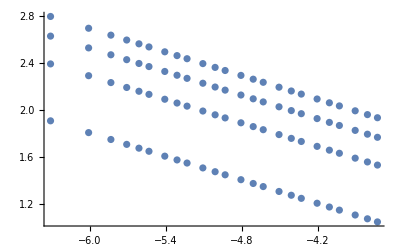

```mathematica
Show[Table[ListPlot[{Log10[#[[1]]],Log10[Abs[ⅈ ω[#[[1]],l]-#[[2]]]]} & /@ Take[KerraOmegaList[l,0,{0,2},Im],tak[[l]]] ],{l,2,5}],PlotRange->All]
```

```mathematica
Fit[{Log10[#[[1]]],Log10[Abs[Alm[#[[1]],2]-#[[2]]]]} & /@ Take[KerraAList[2,0,{0,2},Re],tak[[2]]] ,{1,la},la]
```

-1.473017700230292205441426450774079181793959-0.0648139510490635427113051160121550725448515 la

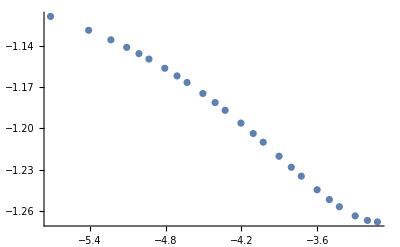

```mathematica
ListPlot[{Log10[#[[1]]],Log10[Abs[Alm[#[[1]],2]-#[[2]]]]} & /@ Take[KerraAList[2,0,{0,2},Re],tak[[2]]] ]
```

```mathematica
Rationalize[1.625]
```

13/8

```mathematica
106/24
```

53/12

```mathematica
N[12/8]
```

1.5

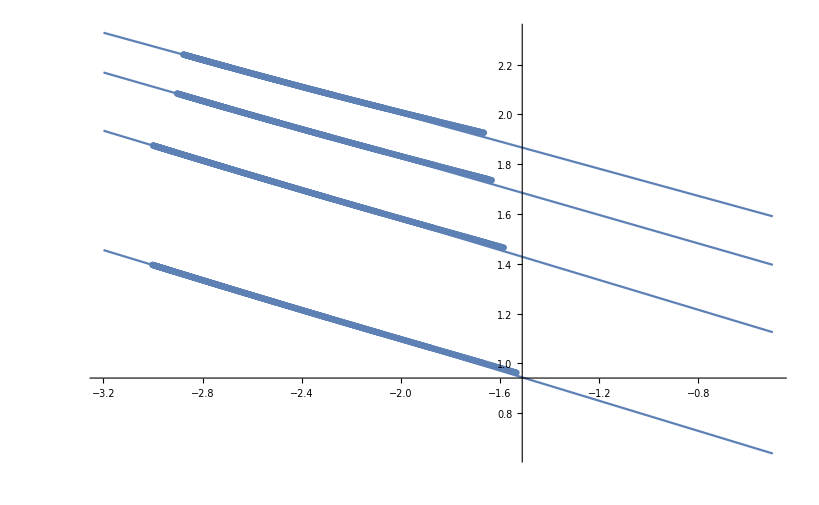

```mathematica
Show[Table[ListPlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ Drop[KerraAList[l,0,{0,2},Re],drp[[l]]],PlotRange->All],{l,2,5}],Plot[Table[ftA[[t]][a],{t,1,4}],{a,-3.2,-0.5},PlotRange->All],PlotRange->All]
```

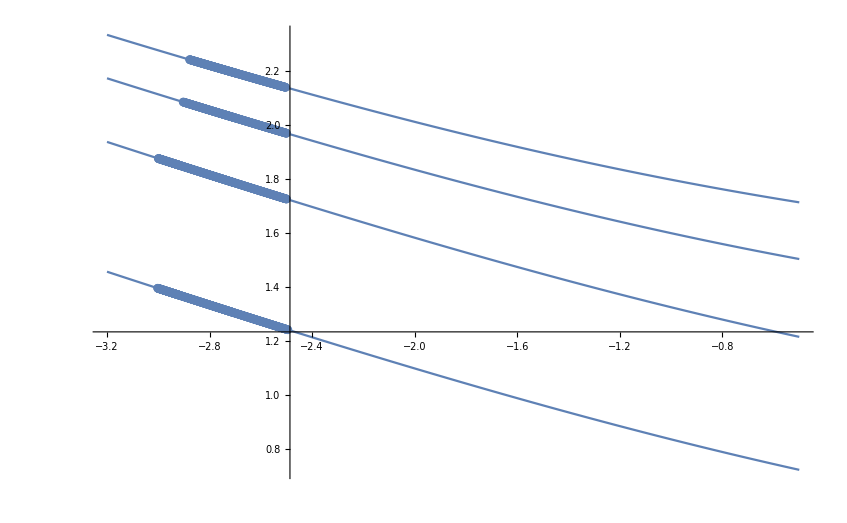

```mathematica
Show[Table[ListPlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ Drop[KerraAList[l,0,{0,2},Re],drp[[l]]],PlotRange->All],{l,2,5}],Plot[Table[Log10[ftA3[[t]][10^la]],{t,1,4}],{la,-3.2,-0.5},PlotRange->All],PlotRange->All]
```

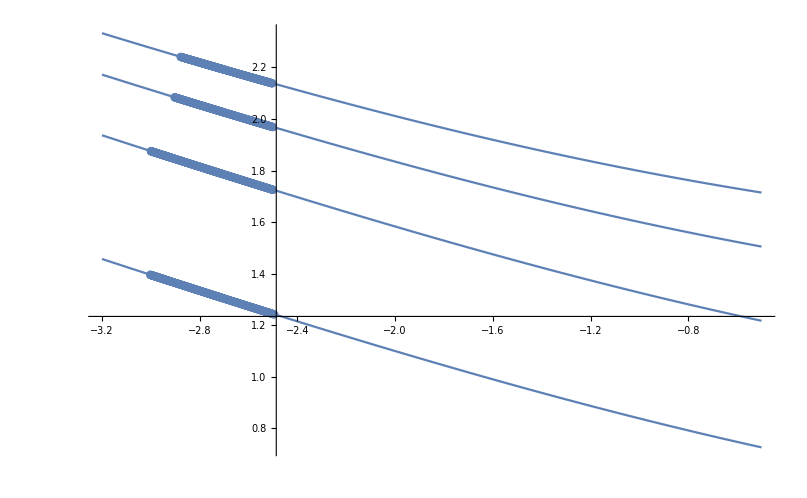

```mathematica
Show[Table[ListPlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ Drop[KerraAList[l,0,{0,2},Re],drp[[l]]],PlotRange->All],{l,2,5}],Plot[Table[Log10[(2l-3)(2^(2/3)3^(1/3)(10^la)^(-1/3)+(4/3 l-2))+0.0624+1.62 l-0.5 l^2],{l,2,5}],{la,-3.2,-0.5},PlotRange->All],PlotRange->All]
```

```mathematica
SchTTMRTable[2]=2;
SchTTMRTable[2,0]={0.001-2.001*I,0,0,0,0};
SchTTMRTable[2,1]={0.347-0.272*I,0,0,0,0};
SchTTMRTable[3]=2;
SchTTMRTable[3,0]={0.6-0.09*I,0,0,0,0};
SchTTMRTable[3,1]={0.6-0.28*I,0,0,0,0};
```

```mathematica
SchwarzschildTTMR[2,0,RadialDebug->1,SchDebug->0]
```

Computing (l=2,n=0)

δω=-0.000999500249999850200753259+0.000999999750249789883540794 ⅈ  root=0.814790684129320946548078

δω=-0.000293026998100418974970208+0.000292716642161629024499628 ⅈ  root=0.23860453352994433170791

δω=-4.288693947742206947529×10^-8-4.54463368441212505051966×10^-11 ⅈ  root=0.0000247028910080702197045188

KerrModes`Private`RadialLentzStep::pflag: Set $MinPrecision =32

δω=9.7452714890090918815619276061311×10^-19-4.5982187813861510023011623265972×10^-16 ⅈ  root=2.6485799663426761104701342344683×10^-13

KerrModes`Private`RadialLentzStep::pflag: Set $MinPrecision =48

δω=-2.24054451963581808753211165981620722065411131357×10^-34+5.28588024779398388053929234951524909564301604718×10^-32 ⅈ  root=3.04469437418045907328422309495722749033891767611×10^-29

SetPrecision::precsm: Requested precision 24 is smaller than $MinPrecision. Using $MinPrecision instead.

KerrModes`Private`RadialLentzStep::increase: Excessive increase in Precision, Abort

$Aborted

```mathematica
$MinPrecision=24
```

24

```mathematica
Plot3D[Abs[PlotContFrac[0,2,0,0,0,ωr -ⅈ ωi,300,15]],{ωr,-0.001,0.001},{ωi,1.999,2.001}]
```

-Graphics3D-

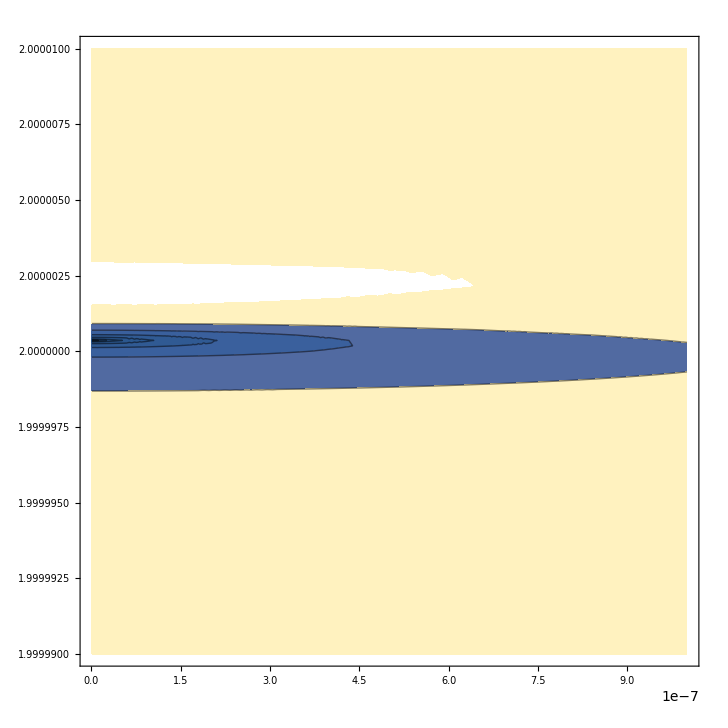

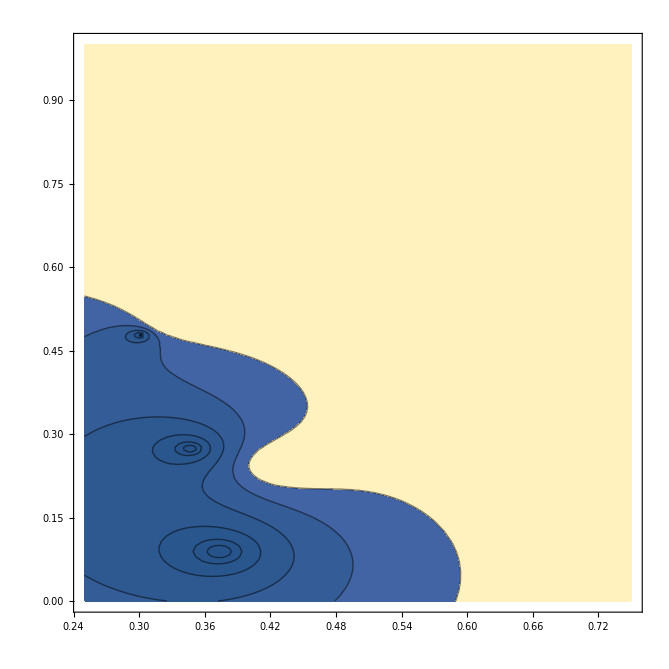

```mathematica
ContourPlot[Abs[PlotContFrac2[0,2,0,1/2^11,1,ωr-ⅈ ωi,300,15]],{ωr,10^(-9),10^-6},{ωi,2-10^(-5),2+10^(-5)},Contours->{1/8,1/4,1/2,1,2,4,8}]
```

```mathematica
Plot3D[{Re[PlotContFrac2[0,2,0,0,1,ωr-ⅈ ωi,300,15]],Im[PlotContFrac2[0,2,0,0,1,ωr-ⅈ ωi,300,15]]},{ωr,0.037,0.0374},{ωi,0.092,0.096}]
```

-Graphics3D-

```mathematica
Plot3D[{Re[RadialCFRem[0,-2,0,0,4,ωr-ⅈ ωi,300][[1]]],Im[RadialCFRem[0,-2,0,0,4,ωr-ⅈ ωi,300][[1]]]},{ωr,0,4},{ωi,0,4}]
```

-Graphics3D-

```mathematica
RadialCFRem[0,-2,0,0,10,-ⅈ 10,2]
```

{0,2}

```mathematica
RadialCFRem[0,2,0,0,4,0.0372-ⅈ 0.094,300]
```

RadialCFRem[0,2,0,0,4,0.0372-0.094 ⅈ,300]

```mathematica
SchwarzschildTTMR[2,0,RadialDebug->1,SchDebug->0]
```

Computing (l=2,n=0)

δω= 0.00156291110201406828110118+0.00510613133482066957985743 ⅈ root= 0.12030556005741694101633

δω= 0.00130855158078940489317997+0.00412714276147985338306565 ⅈ root= 0.0977524363525932384858621

δω= 0.00103594454167295373056286+0.00315551654631708473720952 ⅈ root= 0.0751502749571679139297367

δω= 0.000745337167685731180102232+0.00219159174910191306407745 ⅈ root= 0.0524976796308841772827079

δω= 0.000436730897733925209220932+0.00123578115660854151841983 ⅈ root= 0.0297932642238750083975482

δω= 0.000109336118593342555606563+0.000288786234059965613085436 ⅈ root= 0.00703591413375007183401605

δω= 3.29490029123822078502697×10^-7-2.55383024386891230341558×10^-7 ⅈ root= 9.50610609708662277090294×10^-6

δω= -2.37458595949650936754899×10^-13+7.20240046897876565259863×10^-13 ⅈ root= 1.72934939254777430405789×10^-11

δω= -4.45247939405721967128392×10^-23+1.16248025941627939815106×10^-22 ⅈ root= 2.83863477339011706241109×10^-21

{0.373671684418041835793492-0.0889623156889356982804609 ⅈ,0,300,-14,1.24483174809995174176253×10^-22}

```mathematica
SchwarzschildTTMR[2,1,RadialDebug->0,SchDebug->0]
```

Computing (l=2,n=1)

{0.346710996879163439717677-0.273914875291234817349562 ⅈ,1,300,-14,3.03397134986387404478357×10^-21}

```mathematica
SchwarzschildTTMR[2,7]
```

Computing (l=2,n=2)

{0.301053454612366393764361-0.478276983223071809827295 ⅈ,2,300,-14,3.50976556069587809302063×10^-22}

Computing (l=2,n=3)

{0.251504962185590392029622-0.705148202433496003430767 ⅈ,3,300,-14,1.25435674943564289526196×10^-21}

Computing (l=2,n=4)

{0.207514579813070544996171-0.946844890866355732712142 ⅈ,4,417,-14,1.853460004231019771871×10^-23}

Computing (l=2,n=5)

{0.169299403093043721217619-1.19560805413584821014624 ⅈ,5,772,-14,1.1984630984649905188328×10^-21}

Computing (l=2,n=6)

{0.133252340245187704204216-1.4479106261620379511222 ⅈ,6,1425,-14,1.48902912475939482549437×10^-19}

Computing (l=2,n=7)

{0.0928223336702009444280507-1.70384117220613552851653 ⅈ,7,4428,-14,1.26993519011069264142531×10^-17}

```mathematica
?SchwarzschildTTML
```

SchwarzschildTTML[l,n] computes the Quasi-Normal Mode solutions for overtone n of mode l.  The mode is computed to an accuracy of 10^-14.  For given 'l', if solutions with overtones (n-1) and (n-2) have not been computed, then the routine is recersively called for overtone '(n-1).  If no solutions exist for mode l, then the first two overtones of (l-1) and (l-2) are used to extrapolate initial guesses for these modes.

Options:
	 SpinWeight→Null : -2,-1,0
		 The spin weight must be set via a call to SetSpinWeight before any KerrTTML
		 function call.
	 ModePrecision→24
	 JacobianStep→-10
		 The radial solver make use of numerical derivatives.  The relative step size
		 is set to 10^JacobianStep.
	 RadialCFMinDepth→300
		 The minimum value for the Radial Continued Fraction Depth.
	 RadialCFDepth→1
		 The initial Radial Continued Fraction Depth is usually taken from the prior 
		 solution in the sequence.  Fractional values reduce this initial value by that
		 fraction.  Integer values larger than RadialCFMinDepth are used as the new
		  initial value.
	 RadialRelax→1
		 Initial under-relaxation parameter used in Radial Newton iterations.
	 Rootϵ→-14
		 10^Rootϵ is the maximum allowed magnitude for the Radial Continued Fraction.
	 SchDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Schwarzschile iterations.
	 RadialDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Radial Newton iterations.

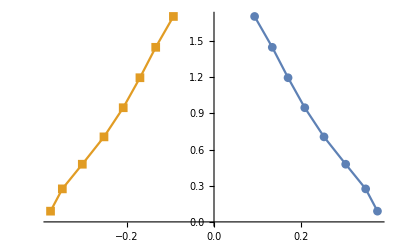

```mathematica
PlotSchTTMR[2]
```

```mathematica
Options[PlotSchTTMR]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,Epilog→{},Filling→None,FillingStyle→Automatic,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→False,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotSpinWeight→-2,PlotStyle→Automatic,KerrModes`Private`PlotTable→Null[],PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},DisplayFunction:>$DisplayFunction,FormatType:>TraditionalForm,PerformanceGoal:>$PerformanceGoal,PlotTheme:>$PlotTheme}

```mathematica
?SchTTMRTable
```

Global`SchTTMRTable

SchTTMRTable[2]=8
 
SchTTMRTable[3]=2
 
SchTTMRTable[2,0]={0.373671684418041835793492-0.0889623156889356982804609 ⅈ,0,300,-14,1.24483174809995174176253×10^-22}
 
SchTTMRTable[2,1]={0.346710996879163439717677-0.273914875291234817349562 ⅈ,1,300,-14,3.03397134986387404478357×10^-21}
 
SchTTMRTable[2,2]={0.301053454612366393764361-0.478276983223071809827295 ⅈ,2,300,-14,3.50976556069587809302063×10^-22}
 
SchTTMRTable[2,3]={0.251504962185590392029622-0.705148202433496003430767 ⅈ,3,300,-14,1.25435674943564289526196×10^-21}
 
SchTTMRTable[2,4]={0.207514579813070544996171-0.946844890866355732712142 ⅈ,4,417,-14,1.853460004231019771871×10^-23}
 
SchTTMRTable[2,5]={0.169299403093043721217619-1.19560805413584821014624 ⅈ,5,772,-14,1.1984630984649905188328×10^-21}
 
SchTTMRTable[2,6]={0.133252340245187704204216-1.4479106261620379511222 ⅈ,6,1425,-14,1.48902912475939482549437×10^-19}
 
SchTTMRTable[2,7]={0.0928223336702009444280507-1.70384117220613552851653 ⅈ,7,4428,-14,1.26993519011069264142531×10^-17}
 
SchTTMRTable[3,0]={0.6-0.09 ⅈ,0,0,0,0}
 
SchTTMRTable[3,1]={0.6-0.28 ⅈ,0,0,0,0}